```mathematica
(* Evaluate Entire Notebook *)
```

```mathematica
(* setup electron distribution function *)
p=Sqrt[g^2-1]
dp=D[p,g]
d3p=4*Pi*p^2*dp
f0=g^(-gp)
gmin=100
gmax=10^5
```

√(-1+g^2)

g/(√(-1+g^2))

4 g √(-1+g^2) π

g^-gp

100

100000

```mathematica
(* obtain electron distribution function normalization *)
Clear[n0]
eq1=n0==A*Integrate[f0,{g,gmin,gmax}]
myA=Solve[eq1,A][[1,1,2]]
f1=f0*myA
(* Check *)
Integrate[f1,{g,gmin,gmax}]
```

n0==(10^(2-5 gp) (-1000+1000^gp) A)/(-1+gp)

(10^(-2+5 gp) (-1+gp) n0)/(-1000+10^(3 gp))

(10^(-2+5 gp) g^-gp (-1+gp) n0)/(-1000+10^(3 gp))

n0

```mathematica
(* factor needed below *)
df1dg=D[f1,g]
```

-(10^(-2+5 gp) g^(-1-gp) (-1+gp) gp n0)/(-1000+10^(3 gp))

```mathematica
(* angle dependent factors *)
(* beta = nuB/nu *)
nperp=Sin[theta]
nz=Cos[theta]
hx=nperp/(beta*eta)*(1-Cos[beta*xi])+I*(sx+Cos[beta*xi]*sxp+eta*Sin[beta*xi]*syp)
hy=Sin[beta*xi]*nperp/beta+I*(sy-eta*Sin[beta*xi]*sxp+Cos[beta*xi]*syp)
hz=xi*nz+I*(sz+szp)
h=Sqrt[hx^2+hy^2+hz^2]
```

Sin[theta]

Cos[theta]

((1-Cos[beta xi]) Sin[theta])/(beta eta)+ⅈ (sx+sxp Cos[beta xi]+eta syp Sin[beta xi])

(Sin[theta] Sin[beta xi])/beta+ⅈ (sy+syp Cos[beta xi]-eta sxp Sin[beta xi])

ⅈ (sz+szp)+xi Cos[theta]

√((ⅈ (sz+szp)+xi Cos[theta])^2+((Sin[theta] Sin[beta xi])/beta+ⅈ (sy+syp Cos[beta xi]-eta sxp Sin[beta xi]))^2+(((1-Cos[beta xi]) Sin[theta])/(beta eta)+ⅈ (sx+sxp Cos[beta xi]+eta syp Sin[beta xi]))^2)

```mathematica
(* angle dependent factors that appear in integral *)
factorh0=Sin[h*p]/h;
factorhik={{D[D[factorh0,sx],sxp],D[D[factorh0,sx],syp],D[D[factorh0,sx],szp]},{D[D[factorh0,sy],sxp],D[D[factorh0,sy],syp],D[D[factorh0,sy],szp]},
{D[D[factorh0,sz],sxp],D[D[factorh0,sz],syp],D[D[factorh0,sz],szp]}};
factorhik=factorhik//.{sx->0,sy->0,sz->0,sxp->0,syp->0,szp->0};
```

```mathematica
(* try to take integral to get alpha *)
wp=20;
pg=3;
ag=Infinity;
gp=2.4 (* choice *)
q=1;
m=1;
c=1;
n0=1; (* pull out this factor *)
eta=-1;
beta=1; (* pull out? *)
integrand=(Sin[theta])*(-I)*q^2/(m*c)*df1dg*Exp[I*xi*g]*factorhik;
integrand=SetPrecision[integrand,wp];
```

```mathematica
(* this is too slow and integrand is highly oscillatory *)
(*alphaik=NIntegrate[integrand,{g,gmin,gmax},{theta,0,Pi},{xi,0,Infinity},WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg]*)
```

```mathematica
(* this is too slow and integrand is highly oscillatory *)
(*alphaik=NIntegrate[integrand,{g,gmin,gmax},{theta,0,Pi},{xi,0,Infinity},WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg]*)
```

```mathematica
(* this is too slow even with integration along angle and limited integration for xi as based upon plotting integrand below *)
(*alphaik=NIntegrate[integrand,{g,gmin,gmax},{theta,0,Pi},{xi,0,1+1*I},WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg]*)
```

```mathematica
(* trying direct integration along angle, no change as could be expected *)
(*integrandnew=integrand//.{xi->xip+I*xip};
alphaik=NIntegrate[integrandnew,{g,gmin,gmax},{theta,0,Pi},{xip,0,1},WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
(*(* try simpler integral, works *)
integrandnew=integrand//.{xi->xip+I*xip,theta->Pi/4};
alphaik=NIntegrate[integrandnew,{g,gmin,10*gmin},{xip,0,1},WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg]*)
```

{{-85.77854991195840475+90.307549498482676539 ⅈ,15.939689492500341164-4.24075746837594197 ⅈ,14.220081795163074508-5.12513832023447283 ⅈ},{-15.939689492404449104+4.240757468473469498 ⅈ,-178.8358824956684903+274.67486829981367805 ⅈ,-92.26607009874695171+184.54609449713364053 ⅈ},{-14.220081795163074508+5.12513832023447283 ⅈ,-92.26607009874695171+184.54609449713364053 ⅈ,-182.0306587584306682+273.84809216995207405 ⅈ}}

```mathematica
(*(* try simpler integral but keep theta, fails to converge *)
integrandnew=integrand//.{xi->xip+I*xip};
alphaik=NIntegrate[integrandnew,{g,gmin,10*gmin},{theta,0,Pi},{xip,0,1},WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg]*)
```

```mathematica
(* try limiting theta from 0 to pi/2 and g up to 10*gmin, works *)
integrandnew=integrand//.{xi->xip+I*xip};
alphaik=NIntegrate[integrandnew,{g,gmin,10*gmin},{theta,0,Pi/2},{xip,0,1},WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg]
```

{{-121.020627690010718+127.79322803212265946 ⅈ,25.796189524903261897-7.334430873243738571 ⅈ,13.643613997849577627-4.811234240062593581 ⅈ},{-25.796189519971041632+7.334430867236431846 ⅈ,-285.8056736155214351+463.63333612382150699 ⅈ,-86.62502780573856547+173.53177476987884725 ⅈ},{-13.643613997849577528+4.811234240053133171 ⅈ,-86.62502780573856547+173.53177476987884916 ⅈ,-221.0793537857010046+307.57086711051635357 ⅈ}}

```mathematica
(*(* try limiting theta from 0 to pi/2 and g up to gmax, fails to converge *)
integrandnew=integrand//.{xi->xip+I*xip};
alphaik=NIntegrate[integrandnew,{g,gmin,gmax},{theta,0,Pi/2},{xip,0,1},WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
(**)
(**)
(**)
(**)
(* below are all just plots to show where behavior has what values, assuming didn't run the above integration yet *)
```

```mathematica
myintegrand=integrand//.{theta->Pi/4};
myintegrand//.{g->gmin,xi->1*I}
```

{{1.4842703064830004 ⅈ,3.0073138374633447,2.4644388766767719},{-3.0073138374633447,6.4131480598365443 ⅈ,5.3329309201349515 ⅈ},{-2.4644388766767719,5.3329309201349515 ⅈ,4.6324265815165843 ⅈ}}

```mathematica
myintegrand=integrand//.{theta->Pi/4,xi->xip*I+xip};
Plot3D[Re[myintegrand[[1,1]]],{g,gmin,gmax},{xip,0,3},PlotPoints->100]
```

-Graphics3D-

```mathematica
Plot3D[Im[myintegrand[[1,1]]],{g,gmin,gmax},{xip,0,3}]
```

Plot3D::plln: Limiting value gmin in {g, gmin, gmax} is not a machine-size real number.

Plot3D[Re[myintegrand⟦1,1⟧],{g,gmin,gmax},{xip,0,10}]

Plot3D::plln: Limiting value gmin in {g, gmin, gmax} is not a machine-size real number.

Plot3D[Im[myintegrand⟦1,1⟧],{g,gmin,gmax},{xip,0,10}]

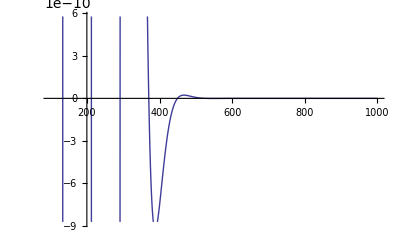

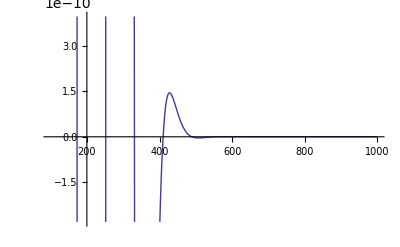

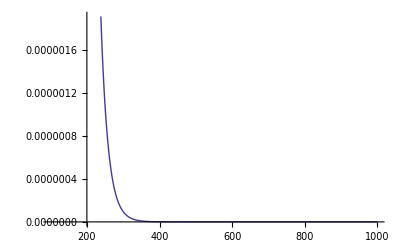

```mathematica
myintegrand=integrand//.{theta->Pi/4};
myintegrand2=myintegrand//.{xi->1*I+1};
Plot[Re[myintegrand2[[1,1]]],{g,100,1000}]
Plot[Im[myintegrand2[[1,1]]],{g,100,1000}]
Plot[Abs[myintegrand2[[1,1]]],{g,100,1000}]
```

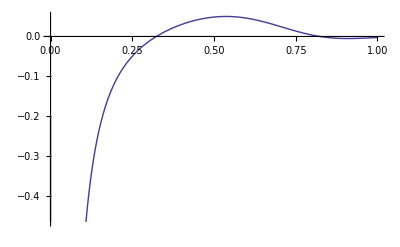

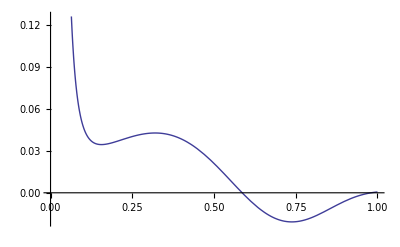

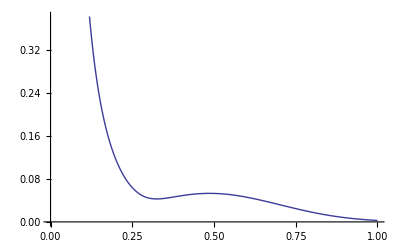

```mathematica
myintegrand3=myintegrand//.{g->100,xi->xip+I*xip};
Plot[Re[myintegrand3[[1,1]]],{xip,0,1}]
Plot[Im[myintegrand3[[1,1]]],{xip,0,1}]
Plot[Abs[myintegrand3[[1,1]]],{xip,0,1}]
```

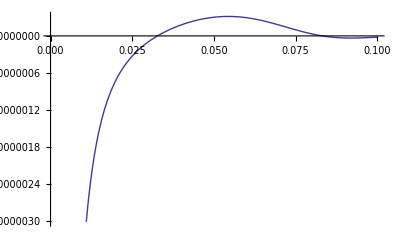

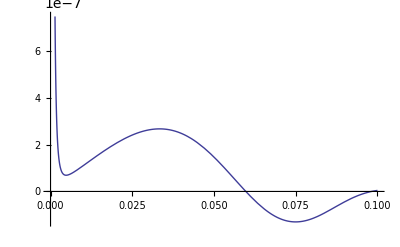

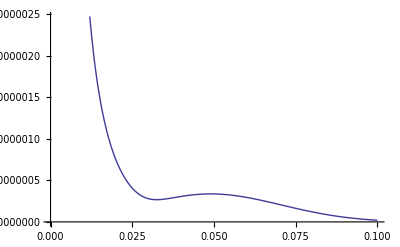

```mathematica
myintegrand3=myintegrand//.{g->gmax,xi->xip+I*xip};
Plot[Re[myintegrand3[[1,1]]],{xip,0,.1}]
Plot[Im[myintegrand3[[1,1]]],{xip,0,.1}]
Plot[Abs[myintegrand3[[1,1]]],{xip,0,.1}]
```